```mathematica
NSolve[{Area1 d1 == Area2 d2, Area1==Entry1,d1==2/3 √(Area1/(√3)),Area2 == √3(f2^2-f1^2),d2==(2(f1^2+f1 f2 + f2^2))/(3(f1+f2)),Area2==Entry2,f1>0,f2>0}/.{Entry1->32/63,Entry2->16/63},{Area1, d1, Area2, d2,f1,f2},Reals]
```

{{Area1→0.507937,d1→0.361022,Area2→0.253968,d2→0.722043,f1→0.669994,f2→0.7717}}

```mathematica
NSolve[{Area1 d1 == Area2 d2, Area1==Entry1,d1==2/3 √(Area1/(√3)),Area2 == √3(f2^2-f1^2),d2==(2(f1^2+f1 f2 + f2^2))/(3(f1+f2)),Area2==Entry2,f1>0,f2>0}/.{Entry1->8/63,Entry2->4/63},{Area1, d1, Area2, d2,f1,f2},Reals]
```

{{Area1→0.126984,d1→0.180511,Area2→0.0634921,d2→0.361022,f1→0.334997,f2→0.38585}}

```mathematica
NSolve[{Area1 d1 == Area2 d2, Area1==Entry1,d1==2/3 √(Area1/(√3)),Area2 == √3(f2^2-f1^2),d2==(2(f1^2+f1 f2 + f2^2))/(3(f1+f2)),Area2==Entry2,f1>0,f2>0}/.{Entry1->2/63,Entry2->1/63},{Area1, d1, Area2, d2,f1,f2},Reals]
```

{{Area1→0.031746,d1→0.0902554,Area2→0.015873,d2→0.180511,f1→0.167499,f2→0.192925}}

```mathematica
NSolve[{Area1 d1 == Area2 d2, Area1==Entry1,d1==2/3 √(Area1/(√3)),Area2 == √3(f2^2-f1^2),d2==(2(f1^2+f1 f2 + f2^2))/(3(f1+f2)),Area2==Entry2,f1>0,f2>0,Area1==√3 h^2,h>0}/.{Entry1->32/63,Entry2->16/63},{Area1, d1, Area2, d2,f1,f2,h},Reals]
```

{{Area1→0.507937,d1→0.361022,Area2→0.253968,d2→0.722043,f1→0.669994,f2→0.7717,h→0.541532}}

```mathematica
MaxF2 = 0.7717001812857543
```

0.7717

```mathematica
({c1=2/(√3)e1,c2=2/(√3)e2}/2)/.{e1->0.3292555141346251,e2->0.4262904097973017}
```

{0.190096,0.246119}

```mathematica
({c1=2/(√3)f1,c2=2/(√3)f2}/2)/.{f2->0.7717001812857543,f1->0.7475720766908822}
```

{0.431611,0.445541}

```mathematica
NSolve[{Area1 d1 == Area2 d2,Area1==√3 (-e1^2+e2^2),d1==(2 (e1^2+e1 e2+e2^2))/(3 (e1+e2)),Area1==Entry1,e1>0,e2>0,Area2 == √3(f2^2-f1^2),d2==(2(f1^2+f1 f2 + f2^2))/(3(f1+f2)),Area2==Entry2,f1>0,f2>0,f2==MaxF2}/.{Entry1->8/63,Entry2->4/63},{Area1, d1, e1,e2,Area2, d2,f1,f2},Reals]
```

{{Area1→0.126984,Area2→0.0634921,f2→0.7717,f1→0.747572,d2→0.7597,d1→0.37985,e1→0.329256,e2→0.42629}}

```mathematica
NSolve[{Area1 d1 == Area2 d2,Area1==√3 (-e1^2+e2^2),d1==(2 (e1^2+e1 e2+e2^2))/(3 (e1+e2)),Area1==Entry1,e1>0,e2>0,Area2 == √3(f2^2-f1^2),d2==(2(f1^2+f1 f2 + f2^2))/(3(f1+f2)),Area2==Entry2,f1>0,f2>0,f2==MaxF2}/.{Entry1->2/63,Entry2->1/63},{Area1, d1, e1,e2,Area2, d2,f1,f2},Reals]
```

{{Area1→0.031746,Area2→0.015873,f2→0.7717,f1→0.765739,d2→0.768724,d1→0.384362,e1→0.372313,e2→0.396164}}

{{0.,0.},{-1.05337,-1.82404},{1.05337,-1.82404}}

{{1.3024,2.35577},{-1.3024,2.35577},{1.50096,2.59808},{-1.50096,2.59808}}

{{1.27858,-0.000150859},{0.639162,1.10736},{1.65552,-0.000142185},{0.827638,1.4338}}

{{-2.90529,-0.00250065},{-1.45481,-2.51481},{-3.00048,0.000832361},{-1.49952,-2.59891}}

{{-0.722418,1.25258},{-1.44598,-0.000657804},{-0.768809,1.33377},{-1.53948,-0.00107631}}

{{1.48876,-2.57715},{2.97626,-0.000729519},{1.49952,-2.59891},{3.00048,0.000832361}}

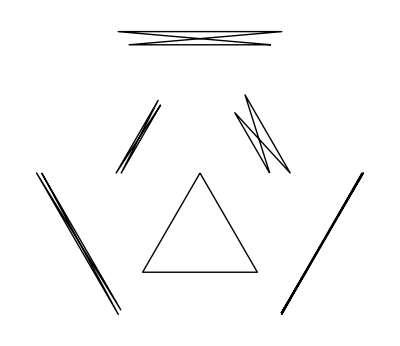

```mathematica
Face1 = { {0,0},{-0.313,-0.542},{0.313,-0.542}};
Face2 = { {-0.387,-0.7}, {0.387,-0.7}, {-0.446,-0.772}, {0.446, -0.772}};
Face3 = { {-0.190,-0.329}, {0.190,-0.329}, {-0.246,-0.426}, {0.246, -0.426}};
Face4 = { {-0.431,-0.748}, {0.431,-0.748}, {-0.446,-0.772}, {0.446, -0.772}};
Face5 = { {-0.215,-0.372}, {0.215,-0.372}, {-0.229,-0.396}, {0.229, -0.396}};
Face6 = { {-0.442,-0.766}, {0.442,-0.766}, {-0.446,-0.772}, {0.446, -0.772}};

scalingFactor = (3/(2/(√3)*.772));
Face1 = Map[RotationTransform[0],Face1]*scalingFactor
Face2 = Map[RotationTransform[π],Face2]*scalingFactor
Face3 = Map[RotationTransform[π/3*2],Face3]*scalingFactor
Face4 = Map[RotationTransform[-π/3],Face4]*scalingFactor
Face5 = Map[RotationTransform[-π/3*2],Face5]*scalingFactor
Face6 = Map[RotationTransform[π/3],Face6]*scalingFactor

Graphics[{Line[Append[Face1,Face1[[1]]]],Line[Append[Face2,Face2[[1]]]],Line[Append[Face3,Face3[[1]]]],Line[Append[Face4,Face4[[1]]]],Line[Append[Face5,Face5[[1]]]],Line[Append[Face6,Face6[[1]]]]}]
```

```mathematica
In the picture, the Order of the Faces From The Bottom Triangle Going Clockwise is: (1,4,5,2,3,6).  In the List of coordinates, printed out above the picture The order is just (1,2,3,4,5,6).
```